Supplementary code for manuscript “Oscillations in the radiative damping of plasma resonances in a gated disk of 2D electron gas”

The main equations for the axisymmetric mode

We solve the following equation
j(r)=σ E^ext(r)+ⅈ (2π σ)/ω(∂^2/(∂r^2)+1/r ∂/(∂r)-1/r^2+ω^2/c^2 | 0
0 | ω^2/c^2)∫_0^R  G(r,r')j(r') r'ⅆr',
with the boundary conditions j_r(R)=0, where
G(r,r')=∫_0^∞ p/(√(p^2-ω^2/c^2))(1-ⅇ^(-2 √(p^2-ω^2/c^2)d))J_1(p r)J_1(p r')ⅆp, σ=(n e^2 τ)/(m(1-ⅈ ω τ)).
We choose the radial external field E^ext so for the current components  j_θ(r)=0 and
j_r(r)=σ Ε_r^ext(r)+ⅈ (2π σ)/ω(∂^2/(∂r^2)+1/r ∂/(∂r)-1/r^2+ω^2/c^2)∫_0^R  G(r,r')j_r(r') r'ⅆr'.
We expand the current in the following series 
j_r(r)=∑_(n=1)^N C_n r/R(1-r^2/R^2)^n.
These basis polynomials satisfy the boundary condition and the parity of the kernel G(r,r').

The system of linear equations for the expansion coefficients C_n

We use the dimensionless parameters
ω̃=(ω R)/c, σ̃=σ/c=1/(2π)(Γ̃)/(γ̃-ⅈ ω̃), r̃=r/R.
Using the parameters and applying the differential operator (∂^2/(∂r^2)+1/r ∂/(∂r)-1/r^2+ω^2/c^2) to the kernel G(r,r') we get the equation for the current
j_r(r̃)=σ̃ c Ε_r^ext(r̃)-ⅈ (2π σ̃)/(ω̃)∫_0^1  (∫_0^∞ p √(p^2-ω^2/c^2)(1-ⅇ^(-2 √(p^2-(ω̃)^2)d̃))J_1(p r̃)J_1(p r̃')ⅆp)j_r(r̃') r̃'ⅆr̃'.      (1)
Let E^dip(r) be the field of the point dipole placed in the point (0, 0, h) with the dipole moment D=(0, 0, D)^T in cylindrical coordinates (r, θ, z). In the case, we have
E^dip(ρ)=((3n(n,D)-D)/Abs[ρ-h]^3-ⅈ ω/c(3n(n,D)-D)/Abs[ρ-h]^2-ω^2/c^2(n(n,D)-D)/Abs[ρ-h])ⅇ^(ⅈ ω/c Abs[ρ-h])=(E_r^dip(r,z), 0, E_z^dip(r,z)), where ρ is the radius vector, h=(0, 0, h)^T, n=(ρ-h)/Abs[ρ-h].
E^ext(ρ)=E^dip(ρ)+E^dip(ρ-2d+2h), where d=(0, 0, -d)^T.
In the dimensional view 
E^dip(ρ̃)=D/R^3((3ñ(ñ,n_D)-n_D)/Abs[ρ̃-h̃]^3-ⅈ ω̃(3ñ(ñ,n_D)-n_D)/Abs[ρ̃-h̃]^2-(ω̃)^2(ñ(ñ,n_D)-n_D)/Abs[ρ̃-h̃])ⅇ^(ⅈ ω̃ Abs[ρ̃-h̃]), n=(ρ̃-h̃)/Abs[ρ̃-h̃].
E^ext(r̃)=(E_0(FE_r(r̃), 0, FE_z(r̃)))^T, where E_0=D/R^3 and has the dimension of an electric field.
Below we write all the dimensional parameters without the tilde-symbol and use only the in plane component of the external field E_r^ext(r)=E_0 FE(r).
We consecutively multiply the current equation (1) by the basis functions (r(1-r^2))^m and integrate it over r with weight function r from 0 to 1. It results in
∑_(n=1)^N {∫_0^1 r (r(1-r^2))^m(r(1-r^2))^n ⅆr}C_n=σ c E_0∫_0^1 r (r(1-r^2))^m FE_r(r)ⅆr-ⅈ (2π σ)/ω∑_(n=1)^N {∫_0^∞ p √(p^2-ω^2/c^2)(1-ⅇ^(-2 √(p^2-(ω̃)^2)d̃))[∫_0^1 rJ_1(p r)(r(1-r^2))^m ⅆr][∫_0^1 rJ_1(p r)(r(1-r^2))^n ⅆr]ⅆp}C_n.
We divide it into the following parts 
ML[n,m]=∫_0^1 r (r(1-r^2))^m(r(1-r^2))^n ⅆr,
MRFin[m,n]=-ⅈ (2π σ)/ω(-ⅈ)∫_0^ω p√(ω^2/c^2-p^2)[∫_0^1 rJ_1(p r)(r(1-r^2))^m ⅆr][∫_0^1 rJ_1(p r)(r(1-r^2))^n ⅆr]ⅆp,
MRFinD[m,n]=- ⅈ(2π σ)/ω(-ⅈ)∫_0^ω p √(ω^2/c^2-p^2)(-ⅇ^(-2 √(p^2-(ω̃)^2)d̃))[∫_0^1 rJ_1(p r)(r(1-r^2))^m ⅆr][∫_0^1 rJ_1(p r)(r(1-r^2))^n ⅆr]ⅆp,
MRInf[m,n]=-ⅈ (2π σ)/ω∫_ω^∞ p√(p^2-ω^2/c^2)[∫_0^1 rJ_1(p r)(r(1-r^2))^m ⅆr][∫_0^1 rJ_1(p r)(r(1-r^2))^n ⅆr]ⅆp,
MRInfD[m,n]=-ⅈ (2π σ)/ω∫_ω^∞ p √(p^2-ω^2/c^2)(-ⅇ^(-2 √(p^2-(ω̃)^2)d̃))[∫_0^1 rJ_1(p r)(r(1-r^2))^m ⅆr][∫_0^1 rJ_1(p r)(r(1-r^2))^n ⅆr]ⅆp,
B[m]=σ ∫_0^1 r (r(1-r^2))^m FE_r(r)ⅆr.
Thus, we arrive to the system
∑_(n=1)^∞ (ML[n,m]-MRFin[n,m]-MRFinD[n,m]-MRInf[n,m]-MRInfD[n,m])C_n=c E_0 B[m].

The absorption power

The average absorption power is given the following integral over the surface disk
P=⟨∫(Re[j(r)ⅇ^(-ⅈ ω t)],Re[j(r) ⅇ^(-ⅈ ω t)])ⅆS⟩=1/2∫(Re[j(r)]Re[E(r)]+Im[j(r)]Im[E(r)])ⅆS=1/2∫Re[(j(r),E^*(r))]ⅆS=π R^2∫_0^1 ∫Re[j_r(r)E_r^*(r)]rⅆr=π R^2∫_0^1 ∫Re[j_r(r)(j_r^*(r))/(c σ^*)]rⅆr=π R^2∫_0^1 ∫Re[j_r(r)(j_r^*(r))/(c σ^*)]rⅆr=(π R^2)/c Re[1/σ]∫_0^1 Abs[j_r(r)]^2 rⅆr=(π R^2)/c Re[1/σ]∑_(n=1,m=1)^(N,N) C_n C_m^*∫_0^1 (r(1-r^2))^n(r(1-r^2))^m rⅆr=(π R^2)/c Re[1/σ]∑_(n=1,m=1)^(N,N) C_n C_m^*ML[n,m].

The average Poynting vector of the electromagnetic dipole field in the disk plane z=0 is
S(r)=c/(4π)⟨[Re[E^dip(r)ⅇ^(-ⅈ ω t)]×Re[H^dip(r) ⅇ^(-ⅈ ω t)]]⟩=c/(8π)Re[[E^dip(r)×(H^dip)^*(r)]],
where the magnetic field H^dip(r)=[n×(E^dip(ρ)+n_D/Abs[ρ-h]^3 ⅇ^(ⅈ ω Abs[ρ-h]))]_(z=0)~c E_0.
The average power of the electromagnetic fields emitted by the point dipole into the disk is
P^dip=2π R^2∫_0^1 (S,n_disk)rⅆr=-2π R^2∫_0^1 S_z(r)rⅆr~c^2 R^2 Abs[E_0]^2 .

Thus the absorption coefficient is A=P/P^dip and does not depend on the c,  E_0 and R. Therefore without loss of generality we put c=1,  E_0=1, and R=1.

The numerical scheme

The conductivity in Drude model

```mathematica
σ[ω_,γ_,Γ_]=1/(2π)Γ/(γ-ⅈ ω);
```

The basis function

```mathematica
fr[n_,x_]:=2^n n^3 x(1-x^2)^n;
```

Below we involve the external electromagnetic field as the field of the oscillating point dipole. Let the dipole place across the z-axis. In the case, the field θ-component equals zero.

The direction of the point dipole in the coordinates (r, z)

```mathematica
nD={0,1};
```

The radius-vector to the point (r, z)

```mathematica
ρv={r,z};
```

The radius-vector to the point dipole

```mathematica
hv={0,h};
```

The normalized direction from the point dipole to the point (r, z)

```mathematica
nv=(ρv-hv)/(√((ρv-hv).(ρv-hv)));
```

The radius-vector to the metal

```mathematica
dv={0,-d};
```

The dipole field in the point (r, z)

```mathematica
Εext[r_,z_,ω_,d_,h_]=((3nv*(nv.nD)-nD)/(√((ρv-hv).(ρv-hv)))^3-ⅈ ω (3nv*(nv.nD)-nD)/(√((ρv-hv).(ρv-hv)))^2-ω^2(nv*(nv.nD)-nD)/(√((ρv-hv).(ρv-hv))))Exp[ⅈ ω √((ρv-hv).(ρv-hv))];
```

The field r-component in the disk plane z=0

```mathematica
Ε1[r_,ω_,d_,h_]=Εext[r,0,ω,d,h][[1]];
```

The Poynting vector of the electromagnetic field emitted by the point dipole

```mathematica
S1[r_,ω_,d_,h_]=1/(8π)ComplexExpand[Re[nv *(Εext[r,0,ω,d,h].Conjugate[Εext[r,0,ω,d,h]+(nD Exp[ⅈ ω √((ρv-hv).(ρv-hv))])/(√((ρv-hv).(ρv-hv)))^3])-Conjugate[Εext[r,0,ω,d,h]+(nD Exp[ⅈ ω √((ρv-hv).(ρv-hv))])/(√((ρv-hv).(ρv-hv)))^3]*(Εext[r,0,ω,d,h].nv)]]/.{z->0}//FullSimplify;
```

The r-component of the field reflected by the metal in the disk plane z=0

```mathematica
Ε2[r_,ω_,d_,h_]=Εext[r-2dv[[1]]+2hv[[1]],0-2dv[[2]]+2hv[[2]],ω,d,h][[1]];
```

The r-component of the net external field in the disk plane z=0

```mathematica
Ε[r_,ω_,d_,h_]=Ε1[r,ω,d,h]+Ε2[r,ω,d,h];
```

IxfnBessel is the integral ∫_0^1 r J_1(p r)(r(1-r^2))^n ⅆr

```mathematica
IxfnBessel[n_]=Integrate[r BesselJ[1,p r]fr[n,r],{r,0,1},Assumptions->n>0&&Element[n,Integers]&&p>0];
```

ML, B, MRInf, MRInfD, MRFin and MRFinD are defined in “The system of linear equations for the expansion coefficients C_n”.

```mathematica
ML[n_,m_]=Integrate[r*fr[n,r]fr[m,r],{r,0,1},Assumptions->n>0&&m>0];
B[n_,ω_,d_,h_]=σt Hold[NIntegrate[x*fr[n,x]Ε[x,ω,d,h],{x,0,1},WorkingPrecision->pr]];
MRInf[m_,n_,ω_]=-ⅈ (2π σt)/ω Integrate[p √(p^2-ω^2)IxfnBessel[n]IxfnBessel[m],{p,ω,∞},Assumptions->ω>0];
MRFin[m_,n_,ω_]=-ⅈ (2π σt)/ω(-ⅈ)Integrate[p √(ω^2-p^2)IxfnBessel[n]IxfnBessel[m],{p,0,ω},Assumptions->ω>0];

MRInfD[m_,n_,ω_,d_]=-ⅈ (2π σt)/ω Hold[NIntegrate[p √(p^2-ω^2)(-Exp[-2 √(p^2-ω^2)d])IxfnBessel[n]IxfnBessel[m],{p,ω,∞},Method->"LevinRule",MaxRecursion->20,WorkingPrecision->pr]];
MRFinD[m_,n_,ω_,d_]=-ⅈ (2π σt)/ω(-ⅈ)Hold[NIntegrate[p √(ω^2-p^2)(-Exp[2ⅈ √(ω^2-p^2)d])IxfnBessel[n]IxfnBessel[m],{p,0,ω},Method->"LevinRule",MaxRecursion->20,WorkingPrecision->pr]];
```

The matrix element

```mathematica
Me[m_,n_,ω_,d_]=ML[m,n]-MRFin[m,n,ω]-MRInf[m,n,ω]-MRFinD[m,n,ω,d]-MRInfD[m,n,ω,d];
```

It’s the function to get the average power of the electromagnetic fields emitted by the point dipole into the disk

```mathematica
RadiationFunction[ω_,d_,h_]=2π Integrate[r *(S1[r,ω,d,h].{0,-1}),{r,0,1},Assumptions->h>0];
```

It’s the function to get the average absorption power

```mathematica
PowerFunction[c_,σt_]:=Module[{power=0},
power=1/2 Re[1/σt]2π NSum[c[[n]]ML[n,m]Conjugate[c[[m]]],{n,1,Nc},{m,1,Nc}];
power
];
```

These functions obtain the resonance frequency and its linewidth

```mathematica
PositionMaxPower[power_]:=Module[{left=First[power][[1]],right=Last[power][[1]],int},
int=Interpolation[power][ω];
ω/.(FindMaximum[int,{ω,(left+right)/2,left,right},WorkingPrecision->30][[2]])
];
WidthPower[power_]:=Module[{left=First[power][[1]],right=Last[power][[1]],int,max=PositionMaxPower[power],lp,rp},
int=Interpolation[power][ω];
lp=ω/.FindRoot[int==1/2(int/.{ω->max}),{ω,(left+max)/2,left,max}];
rp=ω/.FindRoot[int==1/2(int/.{ω->max}),{ω,(max+right)/2,max,right}];
rp-lp
];
```

We establish the accuracy of 300 significant digits.

```mathematica
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"``300."&);
```

Here we choose count Nc of the basis functions, the working precision pr for the numerical integrals. M and b are the matrix and the column to get the expansion coefficients. M has a size Nc×Nc, b - Nc.

```mathematica
Nc=5;
pr=MachinePrecision;
M[ω_,d_,σt_]=Table[Me[m,n,ω,d],{m,1,Nc},{n,1,Nc}];
b[ω_,d_,h_,σt_]=Table[B[m,ω,d,h],{m,1,Nc}];
```

The absorption coefficient

```mathematica
A[ω_,d_]:=Module[{Γ=0.16,γ=0.02,ν=ω,h=100,c={},power=0,rad=0},
c=LinearSolve[ReleaseHold[M[ν,d,σ[ν,γ,Γ]]],ReleaseHold[b[ν,d,h,σ[ν,γ,Γ]]]];
power=Re[PowerFunction[c,σ[ν,γ,Γ]]];
rad=Re[RadiationFunction[ν,d,h]];
(*Print[{ν//N,power/rad}];*)
Return[power/rad]
];
```

We construct the massive of the pair “the distance to the metal - the absorption coefficient” and display dependence A(d)

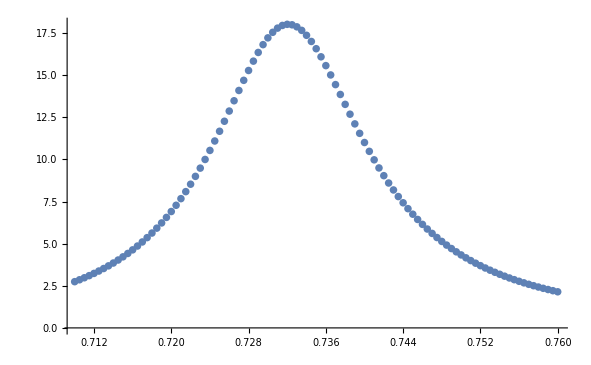

```mathematica
Amas=ParallelMap[{#,A[#,1]}&,Range[0.71,0.76,0.0005]];
ListPlot[Amas,PlotRange->All]
```

Here we can the resonance position and the width

```mathematica
PositionMaxPower[Amas]
WidthPower[Amas]
```

0.732103159621102745413101731856

0.0195119

Data examples

Nr = 5, Γ = 0.16, γ = 0.001, h = 100

The resonance position

```mathematica
expos={{0.001,0.0682914012470706},{0.01,0.209854565158913},{0.04,0.3875079400126447},{0.1,0.537955230001912},{0.2,0.6412114467328865},{0.5,0.7179855436175758},{1,0.7319999895119572},{1.5,0.7334401694797524},{2,0.7337282799436373},{2.5,0.7338381776007413},{3,0.7339060040317431},{3.5,0.7339580387697938},{4,0.7339872497294829},{4.25,0.7339999900521091},{4.5,0.7340115522928673},{5,0.7340008316807793},{5.5,0.7339885055730623},{6,0.7339688012895081},{6.5,0.7339539567428277},{7,0.7339480099273238},{7.5,0.7339502677188264},{8,0.7339558542055388},{8.5,0.7339657767568848},{9,0.7339857506276545},{9.5,0.7339818105011421},{10.,0.7339754778860081},{10.5,0.7339678700246886},{11.,0.7339614628500174},{11.5,0.7339578666760167},{12.,0.7339566237299173},{12.5,0.7339557565663126},{13.,0.733978806215396},{13.5,0.7339803664117948},{14.,0.7339763437440626},{14.5,0.7339715610396432},{15.,0.7339665233871133}};
```

The resonance linewidth

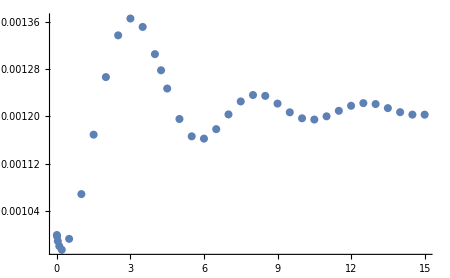
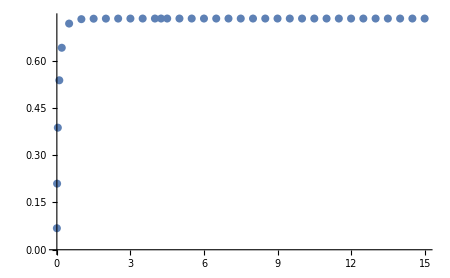

```mathematica
exwid={{0.001,0.0010002697104549846},{0.01,0.0009980500847364404},{0.04,0.0009899882764656809},{0.1,0.0009814882275833714},{0.2,0.0009754200849819705},{0.5,0.000993777655178163},{1,0.0010691879804701765},{1.5,0.0011693571091972998},{2,0.0012663619955853855},{2.5,0.0013367083847115602},{3,0.0013650595236295304},{3.5,0.0013508888572051347},{4,0.0013050500759970163},{4.25,0.0012778518732413646},{4.5,0.0012470976727553262},{5,0.0011957789603528335},{5.5,0.001166526713918703},{6,0.0011626569063897252},{6.5,0.001178660446289892},{7,0.0012034871179538165},{7.5,0.0012253322608376527},{8,0.0012361716796351896},{8.5,0.0012347341872122053},{9,0.0012217097661461063},{9.5,0.001207027941715011},{10.,0.0011969348746537767},{10.5,0.0011948326975063095},{11.,0.0012002544845686192},{11.5,0.0012095604870889787},{12.,0.00121804630407929},{12.5,0.0012224937863998253},{13.,0.001220934573803567},{13.5,0.0012140904362488714},{14.,0.001207264997601376},{14.5,0.0012031049979800423},{15.,0.0012030619330116732}};
Row[{ListPlot[exwid,ImageSize->450,PlotRange->All],ListPlot[expos,ImageSize->450,PlotRange->All]}]
```